# Long-time Limit

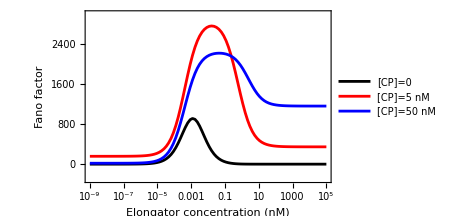

```mathematica
(*************************************** Data export ***************************************)
Off[General::munfl];

(*Parameters*)
r=6; R=30; kfp0=29.1*10^-3; kfm=8.1*10^-5; kfpp0=1.6*10^-3; kfpm=6.2*10^-3; kcp0=12.8*10^-3; kcm=2*10^-4; kcpp0=0.21*10^-3; kcpm=6.2*10^-3;
Id=({{1, 0, 0, 0}, {0, 1, 0, 0}, {0, 0, 1, 0}, {0, 0, 0, 1}});  Iv=({{1}, {0}, {0}, {0}}); 
km[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_]:=({{-(kfp0*F+kcp0*CP), kfm, kcm, 0}, {kfp0*F, -(kfm+kcpp0*CP), 0, kcpm}, {kcp0*CP, 0, -(kcm+kfpp0*F), kfpm}, {0, kcpp0*CP, kfpp0*F, -(kcpm+kfpm)}})
Ret[r_,R_]:=({{r, 0, 0, 0}, {0, R, 0, 0}, {0, 0, 0, 0}, {0, 0, 0, 0}})
 Rem[r_,R_]:=({{r, R, 0, 0}})(*Useful matrices*)

dltv01=({{p1}, {p2}, {p3}, {p4}}); Y=({{1, 1, 1, 1}});
e1[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_]:=km[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP].dltv01 (*Eq (S14)*)
e2=Y.dltv01;

eq1[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_]:=e1[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP][[1,1]]
eq2[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_]:=e1[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP][[2,1]]
eq3[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_]:=e1[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP][[3,1]]
eq4[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_]:=e1[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP][[4,1]]
eq5=e2[[1,1]];
sol[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_]:=Solve[{eq1[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP]==0,eq2[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP]==0,eq3[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP]==0,eq5==1},{p1,p2,p3,p4}]

p11[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_]:=p1/.sol[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP][[1,1]]
p12[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_]:=p2/.sol[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP][[1,2]]
p13[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_]:=p3/.sol[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP][[1,3]]
p14[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_]:=p4/.sol[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP][[1,4]]
dltv0[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_]:=({{p11[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP]}, {p12[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP]}, {p13[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP]}, {p14[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP]}})

dlsv1[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_,r_,R_,s_]:=1/s*Inverse[(s*Id-km[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP])].Ret[r,R].dltv0[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP] (*Subscript[ΔL^(->), s]^(1): Eq. S17 with x=1 *)

dls[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_,r_,R_,s_]:=1/s^2*Rem[r,R].dltv0[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP]//Chop(* <Subscript[ΔL, s]^1>: Eq. S16 with n=1 *)
dl2s[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_,r_,R_,s_]:=1/s^2*Rem[r,R].dltv0[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP]+2/s*Rem[r,R].dlsv1[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP,r,R,s]//Chop(* <Subscript[ΔL, s]^2>: Eq. S16 with n=2 *)


dltm[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_,r_,R_,t_]:=InverseLaplaceTransform[dls[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP,r,R,s],s,t] (* <Subscript[ΔL, t]>: Eq. S18 with n=1 *)
dl2tm[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_,r_,R_,t_]:=InverseLaplaceTransform[dl2s[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP,r,R,s],s,t] (* <Subscript[ΔL, t]^2>: Eq. S18 with n=2 *)


dlt[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_,r_,R_,t_]:=dltm[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP,r,R,t][[1,1]] (* <Subscript[ΔL, t]> *)
dl2t[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_,r_,R_,t_]:=dl2tm[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP,r,R,t][[1,1]] (* <Subscript[ΔL, t]^2> *)
vt[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_,r_,R_,t_]:=dl2t[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP,r,R,t]-(dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP,r,R,t])^2(* Variance *)
ft[kfp0_,kfm_,kcp0_,kcm_,kfpp0_,kfpm_,kcpp0_,kcpm_,F_,CP_,r_,R_,t_]:=vt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP,r,R,t]/dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,CP,r,R,t]

LogLinearPlot[{ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100],ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100],ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,10^-9,100000},Frame->True,FrameStyle->Directive[Black,Thick],PlotStyle->{{Black},{Red},{Blue}},BaseStyle->{FontFamily->"Times",FontSize->15,FontWeight->Bold},FrameLabel->{"Elongator concentration (nM)","Fano factor"},ImageSize->350,PlotLegends->{"[CP]=0","[CP]=5 nM", "[CP]=50 nM"},PlotPoints->100,MaxRecursion->0,PlotRange->{{10^-9,100000},{-300,3000}}]


(*Data Export*)

toEString[dat_]:=If[dat==0.,"0.0000000E+00",MantissaExponent[dat]//With[{mantissa=#[[1]],exponent=#[[2]]},{If[mantissa<0,"-",""],"0.",ToString/@PadRight[First[RealDigits[mantissa,10,Automatic]],16,0],If[exponent<0,"E-","E+"],ToString/@IntegerDigits[exponent,10,2]}//Flatten//StringJoin]&];

Fi=10^-9;Ff1=10^-8;  Ff2=10^-7; Ff3=10^-6; Ff4=10^-5; Ff5=10^-4; Ff6=10^-3; Ff7=10^-2; Ff8=10^-1; Ff9=10^0; Ff10=10^1; Ff11=10^2; Ff12=10^3; Ff13=10^4; Ff14=10^5;
df1=0.9*10^-10; df2=0.9*10^-9; df3=0.9*10^-8; df4=0.9*10^-7; df5=0.9*10^-6; df6=0.9*10^-5; df7=0.9*10^-4; df8=0.9*10^-3; df9=0.9*10^-2; df10=0.9*10^-1; df11=0.9*10^0; df12=0.9*10^1; df13=0.9*10^2; df14=0.9*10^3;



tb11=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Fi,Ff1,df1}];
tb12=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Ff1+df2,Ff2,df2}];
tb13=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Ff2+df3,Ff3,df3}];
tb14=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Ff3+df4,Ff4,df4}];
tb15=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Ff4+df5,Ff5,df5}];
tb16=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Ff5+df6,Ff6,df6}];
tb17=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Ff6+df7,Ff7,df7}];
tb18=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Ff7+df8,Ff8,df8}];
tb19=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Ff8+df9,Ff9,df9}];
tb110=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Ff9+df10,Ff10,df10}];
tb111=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Ff10+df11,Ff11,df11}];
tb112=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Ff11+df12,Ff12,df12}];
tb113=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Ff12+df13,Ff13,df13}];
tb114=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,0,r,R,100]},{F,Ff13+df14,Ff14,df14}];
tb1=Join[tb11,tb12,tb13,tb14,tb15,tb16,tb17,tb18,tb19,tb110,tb111,tb112,tb113,tb114];
tbp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Four-state-model\\GitHub\\F-dl-f-CP0-tau100.dat",tbp1,"FieldSeparators"->"    "];



tb11=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Fi,Ff1,df1}];
tb12=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Ff1+df2,Ff2,df2}];
tb13=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Ff2+df3,Ff3,df3}];
tb14=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Ff3+df4,Ff4,df4}];
tb15=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Ff4+df5,Ff5,df5}];
tb16=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Ff5+df6,Ff6,df6}];
tb17=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Ff6+df7,Ff7,df7}];
tb18=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Ff7+df8,Ff8,df8}];
tb19=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Ff8+df9,Ff9,df9}];
tb110=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Ff9+df10,Ff10,df10}];
tb111=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Ff10+df11,Ff11,df11}];
tb112=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Ff11+df12,Ff12,df12}];
tb113=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Ff12+df13,Ff13,df13}];
tb114=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,5,r,R,100]},{F,Ff13+df14,Ff14,df14}];
tb1=Join[tb11,tb12,tb13,tb14,tb15,tb16,tb17,tb18,tb19,tb110,tb111,tb112,tb113,tb114];
tbp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Four-state-model\\GitHub\\F-dl-f-CP5-tau100.dat",tbp1,"FieldSeparators"->"    "];


tb11=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Fi,Ff1,df1}];
tb12=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Ff1+df2,Ff2,df2}];
tb13=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Ff2+df3,Ff3,df3}];
tb14=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Ff3+df4,Ff4,df4}];
tb15=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Ff4+df5,Ff5,df5}];
tb16=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Ff5+df6,Ff6,df6}];
tb17=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Ff6+df7,Ff7,df7}];
tb18=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Ff7+df8,Ff8,df8}];
tb19=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Ff8+df9,Ff9,df9}];
tb110=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Ff9+df10,Ff10,df10}];
tb111=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Ff10+df11,Ff11,df11}];
tb112=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Ff11+df12,Ff12,df12}];
tb113=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Ff12+df13,Ff13,df13}];
tb114=Table[{F,dlt[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]*0.0027,ft[kfp0,kfm,kcp0,kcm,kfpp0,kfpm,kcpp0,kcpm,F,50,r,R,100]},{F,Ff13+df14,Ff14,df14}];
tb1=Join[tb11,tb12,tb13,tb14,tb15,tb16,tb17,tb18,tb19,tb110,tb111,tb112,tb113,tb114];
tbp1=StringJoin[StringJoin[toEString[#[[1]]]<>"   "<>toEString[#[[2]]]<>"   "<>toEString[#[[3]]]<>"\n"]&/@tb1];
Export["F:\\Colab\\Sandeep\\2-Actin\\Results\\Analytics\\Four-state-model\\GitHub\\F-dl-f-CP50-tau100.dat",tbp1,"FieldSeparators"->"    "];

Quit[];
```